```mathematica
step=0.005;
view=4;
eps=2*step/3;
tiny=N[10^-10];
pts=Select[Tuples[{Range[-1,1,step],Range[-1,1,step]}],Abs[Total[#^2]-1]<eps&];
(*ListPlot[pts,PlotRange->{{-view,view},{-view,view}},AspectRatio->1]*)
slide[{x_,y_},u_]:=With[{t=-u+(1-u)x},{t,(y(t-1))/(x-1+tiny)}];
Manipulate[ListPlot[slide[#,u]&/@pts,PlotRange->{{-view,view},{-view,view}},AspectRatio->1],{u,0,1}]
```

```mathematica
animStep=0.01;
anim=Table[ListPlot[slide[#,u]&/@pts,PlotRange->{{-view,view},{-view,view}},AspectRatio->1],{u,0,1,animStep}];
```

```mathematica
Length@anim
```

101

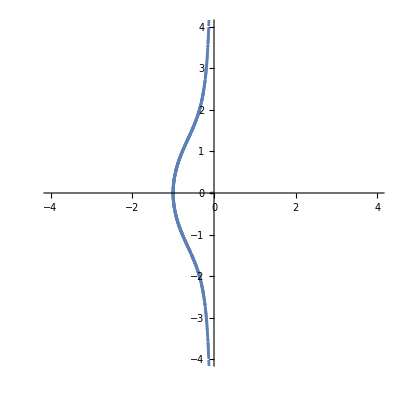

```mathematica
anim[[54]]
```

```mathematica
Export["circ.gif",anim]
```

circ.gif

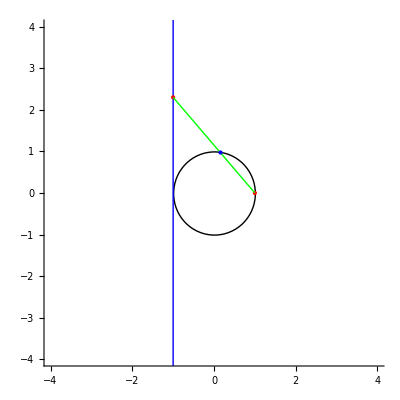

```mathematica
t=2.3;
f[x_]:=-t(x-1)/2;
x=2t^2/(t^2+4)-1;
pic=Graphics[{Circle[],Blue,Line[{{-1,-view-1},{-1,view+1}}],Red,PointSize@Large,Point[{-1,t}],Point[{1,0}],Green,Line[{{-1,t},{1,0}}],Blue,Point[{x,f[x]}]},Axes->True,PlotRange->{{-view,view},{-view,view}},AspectRatio->1]
```

```mathematica
Export["pt.jpg",pic]
```

pt.jpg

```mathematica
intersectionPic[t_]:=With[{x=2t^2/(t^2+4)-1},Graphics[{Circle[],Blue,Line[{{-1,-view-1},{-1,view+1}}],Red,PointSize@Large,Point[{-1,t}],Point[{1,0}],Green,Line[{{-1,t},{1,0}}],Blue,Point[{x,-t(x-1)/2}]},Axes->True,PlotRange->{{-view,view},{-view,view}},AspectRatio->1]];
Manipulate[intersectionPic[u],{u,-100,100}]
```

```mathematica
bigStep=5;
smallStep=0.5;
anim2=Join[Table[intersectionPic[u],{u,-100,-view-1,bigStep}],Table[intersectionPic[u],{u,-view-1,view+1,smallStep}],Table[intersectionPic[u],{u,view+1,100,bigStep}]];
Export["circ2.gif",anim2]
```

circ2.gif

```mathematica
((m/n)^2-4)/((m/n)^2+4)//Simplify
```

(m^2-4 n^2)/(m^2+4 n^2)

```mathematica
(4m/n)/((m/n)^2+4)//Simplify
```

(4 m n)/(m^2+4 n^2)